## Structural complexity of functional response models - Part 2

```mathematica
Clear["Global`*"]
SetDirectory[NotebookDirectory[]]
```

### Preliminaries

SC_2= -Log_ef(x|(Θ̂)_x)+k/2 Log_e(n/(2 π))+Log_e∫_Θ √(det I(Θ))ⅆΘ + o(1)
The first term is the likelihood. 
The second term is dependent on parameter count (k) and sample size (n).
The third term containing I(Θ), the Expected Fisher Information Matrix, reflects the model's flexibility.
The flexibility term by itself can only be compared between models having the same number of parameters.

#### Load results of "FisherMatrix-1_Compute.nb”

Dummy determinants for k=3 models (will be overridden when actual results exist):

```mathematica
DetBD=0; DetCM=0; DetAA=0;
NIntBD=0;NIntCM=0;NIntAA=0;
```

Pick the output that has been successfully computed :

```mathematica
Get["results/FisherMatrix-1_Output_k1"];
```

```mathematica
Get["results/FisherMatrix-1_Output_k1k2"];
```

```mathematica
Get["results/FisherMatrix-1_Output_k1k2k3"];
```

```mathematica
Get["results/FisherMatrix-1_Output_k1k2k3"];
```

```mathematica
Get["results/FisherMatrix-1_Output_k1k2k3_NInt"];
```

```mathematica
Get["results/FisherMatrix-1_Output_k1k2k3_aNInt"];
```

NIntegrate::inumr: The integrand √((25 2^(-1+2 m) a («1») (-(625 a^2 (Times[«2»]+«38»+«1»)^2)/(16 (1+«1»)^6 ((«1»«1»)^6 (1+«1»)^6 (Power[«2»]+«1»)^6)+(15625 «3»)/(16 «3» («1»)^6)) Log[2]^2)/((2^m+10 a h)^3 (2^m+15 a h)^3)-(25 «3» ((«1»)/(«1»)-(«1»)/(«1»)))/((«1»)^3 ((«1»«1»)^3)-(25 «4» (-(625 «4» Log[2])/((1+«1»)^3 «1» «1» («1»)^6)+(«1»)/(«1»)))/((2^m+10 a h)^3 (2^m+15 a h)^3)) has evaluated to non-numerical values for all sampling points in the region with boundaries {{0,1/15},{0,1/15}}.

NIntegrate::inumr: The integrand √((143125 a^2)/((1+5 a h)^6 (1+10 a h)^6 (1+15 a h)^6 (2+15 a h)^6)+«17»+(10840351581573486328125 a^20 h^18)/((1+5 a h)^6 (1+10 a h)^6 (1+15 a h)^6 (2+15 a h)^6)) has evaluated to non-numerical values for all sampling points in the region with boundaries {{0,1/15}}.

NIntegrate::inumr: The integrand √(-(25 (5+«50») ((15625 a^3 (21+2277 a h+«48»+«5») (5+555 a h+«48»+«15»))/(16 (1+«1»+γ)^6 ((«1»«1»)^6 («1»)^6 (1+Times[«1»]+Times[«2»])^6)-(«1»)/(«1»)))/(4 (1+10 a h+γ)^3 (1+15 a h+γ)^3 (1+10 a h+2 γ)^3 (1+15 a h+2 γ)^3)+(«1»)/(«1»)-(25 «2» (-(625 «1»«1»(«1»))/(16 «3» («1»)^6)+«1»))/(4 («1»)^3 («1»)^3 ((«1»«1»)^3 (1+15 a h+2 γ)^3)) has evaluated to non-numerical values for all sampling points in the region with boundaries {{0,1/15},{0,1}}.

General::stop: Further output of NIntegrate::inumr will be suppressed during this calculation.

SetDelayed::write: Tag NIntegrate in NIntegrate[√DetAG,ParmRangeB⟦1⟧,PrecisionGoal→precgoal][α_?NumericQ] is Protected.

SetDelayed::write: Tag NIntegrate in NIntegrate[√DetH2,ParmRangeB⟦1⟧,PrecisionGoal→precgoal][α_?NumericQ] is Protected.

### Second Term dependence on k and n

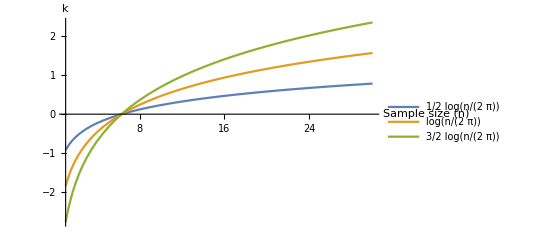

```mathematica
p1=Plot[Evaluate@Table[k/2 Log[n/(2 π)],{k,1,3}],{n,1,30},
PlotLegends->"Expressions",(*{"k=1","k=2","k=3"},*)
AxesLabel->{"Sample size (n)","k"}]
```

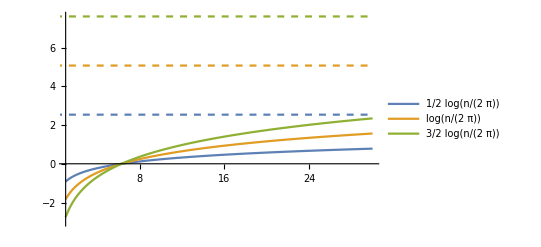

```mathematica
Lims=Limit[Table[k/2 Log[n/(2 π)],{k,1,3}],n-> 1000]//N;
p2=Plot[Lims,{n,0,30},PlotRange->{{1,30},{-3,Max[Lims]}},PlotStyle->Dashed];
p12=Show[p2,p1]
```

```mathematica
Export["results/FisherMatrix-2_Output_ParameterComplexity.jpg",p12];
```

### Third term - Flexibility

```mathematica
Labels={"H1","R","HV","H2","AG","BD","CM","AA"};
NInts={NIntH1,NIntR,NIntHV,NIntH2,NIntAG,NIntBD,NIntCM,NIntAA}
gNInts={NInts[[{1,2}]],
NInts[[{3,4,5}]],
NInts[[{6,7,8}]]
};
rNInts={NInts[[{1,2}]]/NInts[[1]],
NInts[[{3,4,5}]]/NInts[[3]],
NInts[[{6,7,8}]]/NInts[[6]]
};
Export["results/FisherMatrix-2_Output_logNIntegrals.txt",{Νvals,Pvals,Labels,NInts,rNInts}];
```

{13.6717,13.4689,23.1946,23.644,23.9212,31.1702,33.8143,31.7161}

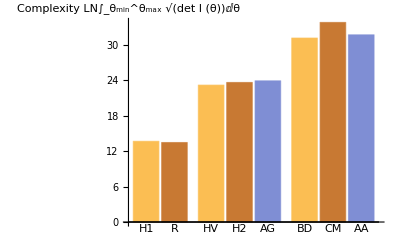

```mathematica
lNInts=TakeList[MapIndexed[Labeled[#,Labels[[#2[[1]]]]]&,Flatten@gNInts],Length/@gNInts];
bc1=BarChart[lNInts,AxesLabel->"Complexity LN∫_θ_min^θ_max √(det I (θ))ⅆθ"];
bc1
Export["results/FisherMatrix-2_Output_Complexity_absolute.jpg",bc1];
```

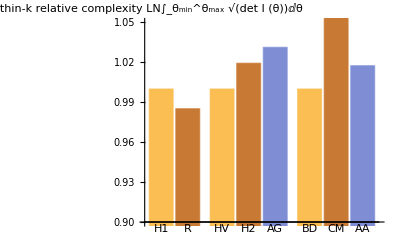

```mathematica
lrNInts=TakeList[MapIndexed[Labeled[#,Labels[[#2[[1]]]]]&,Flatten@rNInts],Length/@rNInts];bc2=BarChart[lrNInts,
PlotRange->{Automatic,{0.9,1.05}},
AxesLabel->"Within-k relative complexity LN∫_θ_min^θ_max √(det I (θ))ⅆθ"];
bc2
Export["results/FisherMatrix-2_Output_Complexity_relative.jpg",bc2];
```

```mathematica
(*
Manipulate[
ParmRange={{a,amin,amax},{h,hmin,hmax},{γ,γmin,γmax},{m,mmin,mmax},{β,βmin,βmax}};
NInts={
Log[NIntegrate[Sqrt[DetH1],ParmRange[[1]]]],
Log[NIntegrate[Sqrt[DetH2],ParmRange[[1]],ParmRange[[2]]]],
Log[NIntegrate[Sqrt[DetBD],ParmRange[[1]],ParmRange[[2]],ParmRange[[3]]]],
Log[NIntegrate[Sqrt[DetCM],ParmRange[[1]],ParmRange[[2]],ParmRange[[3]]]],
Log[NIntegrate[Sqrt[DetR],ParmRange[[1]]]],
Log[NIntegrate[Sqrt[DetHV],ParmRange[[1]],ParmRange[[4]]]],
Log[NIntegrate[Sqrt[DetAG],ParmRange[[1]],ParmRange[[2]]]],
Log[NIntegrate[Sqrt[DetAA],ParmRange[[1]],ParmRange[[2]],ParmRange[[4]]]]
};
BarChart[NInts/NInts[[1]],ChartLabels->{"H1","H2","BD","CM","R","HV","AG","AA"},
AxesLabel->"Complexity relative to Holling Type 1"]
,
{{amin,0.01},0.0001,.01},
{{amax,30},1,100},
{{hmin,0.01},0.0001,0.01},
{hmax,2,100},
{{γmin,0.01},0.0001,0.01},
{γmax,2,100},
{{mmin,0.01},0.0001,0.01},
{mmax,1,100}
]
*)
```

### Partial numeric Integration

Fix ' a', integrate square root of Expected Fisher Information Matrix over remaining parameters , and take natural log.

```mathematica
aNIntH2
```

NIntegrate[√DetH2,ParmRangeB⟦1⟧,PrecisionGoal→precgoal]

```mathematica
ParmRangeB=Drop[ParmRangeA,1];
precgoal=2;
```

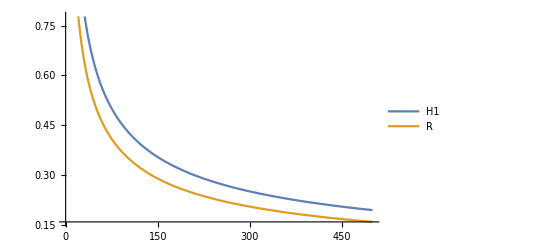

```mathematica
pnk1=Plot[{
aNIntH1,
aNIntR
},
{a,0.01,500},
PlotLegends->Placed[{"H1","R"},Above]];
```

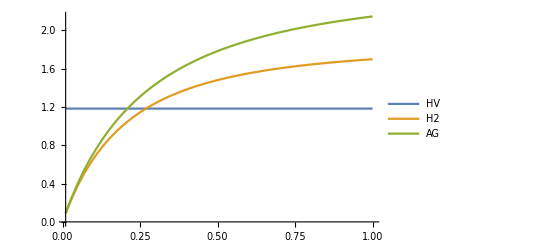

```mathematica
pnk2=Plot[{
aNIntHV,
aNIntH2[a],
aNIntAG[a]
},
{a,0.01,1},
PlotLegends->Placed[{"HV","H2","AG"},Above]];
```

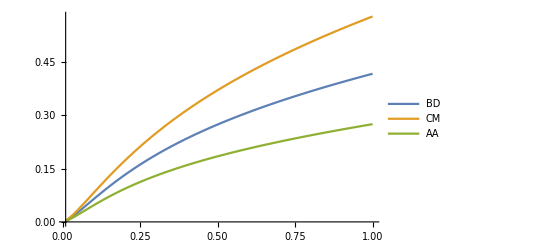

```mathematica
pnk3=Plot[{
aNIntBD[a],
aNIntCM[a],
aNIntAA[a]
},
{a,0.01,1},
PlotLegends->Placed[{"BD","CM","AA"},Above]];
```

```mathematica
pn=GraphicsRow[{pnk1,pnk2,pnk3},ImageSize->Large]
Export["results/FisherMatrix-2_Output_partial_numeric_a.jpg",pn];
```

-Graphics-

#### Save all above results

```mathematica
Save["results/FisherMatrix-2_Ouput_PartialNumeric","`*"];
```

### Symbolic Integration

```mathematica
Sqrt[DetH1]
IntH1=Assuming[a>0,Log[Integrate[Sqrt[DetH1],a]]]//FullSimplify
```

```mathematica
Simplify[Sqrt[DetH2],a>0, h>0]
IntH2a=Assuming[a>0 && h> 0,Log[Integrate[Sqrt[DetH2],a]]]//FullSimplify
IntH2h=Assuming[a>0 && h> 0,Log[Integrate[Sqrt[DetH2],h]]]//FullSimplify
IntH2=Assuming[a>0 && h> 0,Log[Integrate[Sqrt[DetH2],a,h]]]//FullSimplify
```

```mathematica
Sqrt[DetBD];
IntBD=Assuming[a>0 && h> 0 && γ > 0,Log[Integrate[Sqrt[DetBD],a,h,γ]]]//FullSimplify
```

```mathematica
Sqrt[DetCM]
IntCM=Assuming[a>0 && h> 0 && γ > 0,Log[Integrate[Sqrt[DetCM],a,h,γ]]]//FullSimplify
```

```mathematica
Sqrt[DetR]
IntR=Assuming[a>0 ,Log[Integrate[Sqrt[DetR],a]]]//FullSimplify
```

```mathematica
Log[Sqrt[DetHV]]
IntHVa=Assuming[a>0 && m> 0 ,Log[Integrate[Sqrt[DetHV],a]]]//FullSimplify
IntHVm=Assuming[a>0 && m> 0 ,Log[Integrate[Sqrt[DetHV],m]]]//FullSimplify
IntHV=Assuming[a>0 && m> 0 ,Log[Integrate[Sqrt[DetHV],a,m]]]//FullSimplify
```

```mathematica
Sqrt[DetAA];
IntAG=Assuming[a>0 && h> 0, Log[Integrate[Sqrt[DetAG],a,h]]]//FullSimplify
```

```mathematica
Sqrt[DetAA];
IntAA=Assuming[a>0 && h> 0 && m > 0,Log[Integrate[Sqrt[DetAA],a,h,m]]]//FullSimplify
```

```mathematica
Ints={ΝVals,Pvals,IntH1,IntH2,IntBD,IntCM,IntR,IntHV,IntAG,IntAA};
```

```mathematica
Export["results/FisherMatrix-2_Output_Symbolic.txt",Ints];
```

#### Save (or load) all above results

```mathematica
Save["results/FisherMatrix-2_Output","`*"];
```